```mathematica
SetDirectory[NotebookDirectory[](*DirectoryName[$InputFileName]*) ]
Get["corr_proj_funcs.m"]
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v22/bin_v21

## How to Run

1. setup arguments in “config1.txt” & “plotdata_config.txt” 
2. setup data files of samept & grid data in the “control runfunc you want to run” section of the code
3.
a. if this file’s extension is .nb, run “control runfunc you want to run” title at bottom of the code
b. if this file’s extension is .m (script version), type math -script “filename of this file” in the terminal

```mathematica
(*20170514: test new version with shape of point could be choosed*)
(*this version: sampt data use color, highlight size for every points, grid data use the retangle, black color, same size, |corr| > 0.5*)
(*
 PDFCorrelationplot8Here[datain_,titlein_,xtitlein_,ytitlein_,plotrangein_,stretchxin_,stretchyin_,barseperatorin_,legendlabelin_,epilogtextin_,highlightrangein_,unhighlightsizein_]:=
Module[{data=datain,title=titlein,xtitle=xtitlein,ytitle=ytitlein,plotrange=plotrangein,αx=stretchxin,αy=stretchyin,barseperator=barseperatorin,legendlabel=legendlabelin,epilogtext=epilogtextin,highlightrange=highlightrangein,unhighlightsize=unhighlightsizein,
plotxQout,minx,maxx,miny,maxy,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotrangetmp,mycolorscheme,psizebase,psizenorm,p,datalist,drange,barcolor,mybarlegend,barmin,barmax,textsize,outlayertext,
tickslist,tickslog,nolable,Loglable,xTicks,yTicks,p2,AllPlots,
ptshape,ptshaperescale,drawdataset},

(*default*)
minx=0.00001;
maxx=1;
miny=1;
maxy=1100;
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*decide data max range in plot*)

datalist=datain/.LF1[a__]:>Abs[{a}[[3]] ];
drange=0.5+0.5*IntegerPart[Max[datalist]/0.5];

(*color scheme*)
(*
mycolorscheme="AlpineColors";
mycolorscheme="LightTemperatureMap";
*)
mycolorscheme="TemperatureMap";

barseperator=barseperator;
barmin=Min[barseperator];barmax=Max[barseperator];
barcolor=Table[ColorData[{mycolorscheme,{barmin,barmax}}, barmin+(i-0.5)*(barmax-barmin)/(Length[barseperator]-1)],{i,1,Length[barseperator]-1}];
barcolor=Darker[#,0.05]&/@barcolor;(*make color darker*)


(*lowlimit color is at the middle of barcolor*)
barcolor[[(Length[barcolor]+1)/2 ]]=(*ColorData["Atoms","ColorList"][[22]];*)(*ColorData[34,"ColorList"][[4]];*)(*ColorData[49,"ColorList"][[4]];*)ColorData[30,"ColorList"][[5]];
(*make small value data unvisible*)
barcolor[[(Length[barcolor]+1)/2 ]]=Lighter[barcolor[[(Length[barcolor]+1)/2 ]],0.75];

mybarlegend=BarLegend[{barcolor,{barmin,barmax}},barseperator,LegendLabel->legendlabel,LabelStyle->{FontSize->14}];

(*add text to plot by Epilog*)
textsize=16;
(*Npttext=Text[Style["Npt: "<>ToString[Length[data//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];*)
outlayertext={epilogtext};

(*point size normalization*)
psizebase=0.005;
psizenorm=0.01;
p=2.0;(*20170307: make size small*)p=1.5;

(*if want to customize the plot range*)
plotrangetmp=ToString[plotrange];
If[
plotrangetmp!="None",
minx=plotrange[[1]];
maxx=plotrange[[2]];
miny=plotrange[[3]];
maxy=plotrange[[4]];
];


tickslist=Table[Table[j*10.0^i,{j,1,9}],{i,-6,6}]//Flatten;
tickslog=Table[Log[tickslist[[i]]  ],{i,1,11*9}];
nolable={"","","","","","","",""};
Loglable={"\!\(\*SuperscriptBox[\(10\), \(-6\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-5\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-4\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-3\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-2\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-1\)]\)",nolable,"1",nolable,"\!\(\*SuperscriptBox[\(10\), \(1\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(2\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(3\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(4\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(5\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(6\)]\)",nolable}//Flatten;
xTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;
yTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;

(*data structure: 
{ pt1, pt2, pt3, pt4, ...}
ptn == LF1[ x1n, x2n, corr( obsA(x1n), obsB(x2n))]
*)
p2=ListPlot[
{{0.00001,2},{0.99,1200.0}}
(*
datain/.LF1[a__]:>Style[
{Log[{a}[[1]] ],Log[{a}[[2]] ]},
PointSize[(*psizebase+psizenorm*(Abs[{a}[[3]] ]/drange)*)Setpointsize2[{a}[[3]],highlightrange,unhighlightsize] ],(*ColorData[{mycolorscheme,{-drange,drange} }][{a}[[3]]]*)
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*) ] 
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
]*),
AspectRatio->1,
PlotRange->{{Log[minx],Log[maxx]},{Log[miny],Log[maxy]}},
PlotLegends->(*BarLegend[{mycolorscheme,{-drange,drange}}]*)Placed[mybarlegend,{1.0,0.5}],
PlotStyle->White,(*solve bug: system automatically set blue points in plot, -> set blue to white so that we don't see it*)
Epilog->{epilogtext,outlayertext}
 ];

ptshape={"●",(*"*"*)(*"x"*)"□"(*"■"*),"▲","▼","△","▽","○"};
ptshaperescale={750.0,2000.0,850.0,800.0,750.0};
{{"●",8.96},{"■",8.96},{"◆",10.88},{"▲",10.24},{"▼",10.24},{"○",10.24},{"□",10.24},{"◇",10.24},{"△",11.136},{"▽",11.136}};

drawdataset=
Table[
datain[[igroup]]/.LF1[a__]:>Style[
Text[ptshape[[igroup]],{Log[{a}[[1]] ],Log[{a}[[2]] ]}],
(*size*)
If[
igroup==1,
ptshaperescale[[igroup]]*Setpointsize2[{a}[[3]],highlightrange,unhighlightsize],
(*igroup==2: grid data*)ptshaperescale[[igroup]]*0.01
] (*]*),
(*color*)If[
igroup==1,
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*)],
(*igroup==2: grid data*)(*Directive[Darker[Green,0.2], Opacity[0.9]]*)(*Lighter[Black,0.35]*)(*Magenta*)Darker[Green,0.2]
]
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
],
{igroup,1,Length[datain]}
];

AllPlots=Show[
{
p2,
Graphics[
{drawdataset[[2]],drawdataset[[1]]}//Flatten
(*
Table[
datain[[igroup]]/.LF1[a__]:>Style[
Text[ptshape[[igroup]],{Log[{a}[[1]] ],Log[{a}[[2]] ]}],
(*size*)
If[
igroup==1,
ptshaperescale[[igroup]]*Setpointsize2[{a}[[3]],highlightrange,unhighlightsize],
(*igroup==2: grid data*)ptshaperescale[[igroup]]*0.01
] (*]*),
(*color*)If[
igroup==1,
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*)],
(*igroup==2: grid data*)Directive[Gray, Opacity[0.25]]
]
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
],
{igroup,1,Length[datain]}
]//Flatten
*)
]
},
Frame->True,
FrameTicks->{xTicks/. LF->List,xTicks/. LF->List,
xTicks/. LF[a__]:>{{a}[[1]],""},xTicks/. LF[a__]:>{{a}[[1]],""}},
Axes->False,
PlotLabel->Style[title,titlesize,Black],
FrameLabel->{Style[xtitle,xtitlesize,Black],Style[ytitle,ytitlesize,Black]},
ImageSize->imgsize,
AspectRatio->1
];

AllPlots
 ];
 *)
```

```mathematica
PDFCorrelationplot8Here[datain_,titlein_,xtitlein_,ytitlein_,plotrangein_,stretchxin_,stretchyin_,barseperatorin_,legendlabelin_,epilogtextin_,highlightrangein_,unhighlightsizein_]:=
Module[{data=datain,title=titlein,xtitle=xtitlein,ytitle=ytitlein,plotrange=plotrangein,αx=stretchxin,αy=stretchyin,barseperator=barseperatorin,legendlabel=legendlabelin,epilogtext=epilogtextin,highlightrange=highlightrangein,unhighlightsize=unhighlightsizein,
plotxQout,minx,maxx,miny,maxy,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotrangetmp,mycolorscheme,psizebase,psizenorm,p,datalist,drange,barcolor,mybarlegend,barmin,barmax,textsize,outlayertext,
tickslist,tickslog,nolable,Loglable,xTicks,yTicks,p2,AllPlots,
ptshape,ptshaperescale,drawdataset,αxtmp},

(*default*)
minx=0.00001;
maxx=1;
miny=1;
maxy=1100;
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*decide data max range in plot*)

datalist=datain/.LF1[a__]:>Abs[{a}[[3]] ];
drange=0.5+0.5*IntegerPart[Max[datalist]/0.5];

(*color scheme*)
(*
mycolorscheme="AlpineColors";
mycolorscheme="LightTemperatureMap";
*)
mycolorscheme="TemperatureMap";

barseperator=barseperator;
barmin=Min[barseperator];barmax=Max[barseperator];
barcolor=Table[ColorData[{mycolorscheme,{barmin,barmax}}, barmin+(i-0.5)*(barmax-barmin)/(Length[barseperator]-1)],{i,1,Length[barseperator]-1}];
barcolor=Darker[#,0.2]&/@barcolor;(*make color darker*)


(*lowlimit color is at the middle of barcolor*)
barcolor[[(Length[barcolor]+1)/2 ]]=(*ColorData["Atoms","ColorList"][[22]];*)(*ColorData[34,"ColorList"][[4]];*)(*ColorData[49,"ColorList"][[4]];*)ColorData[30,"ColorList"][[5]];
(*make small value data unvisible*)
barcolor[[(Length[barcolor]+1)/2 ]]=Lighter[barcolor[[(Length[barcolor]+1)/2 ]],0.5];
(*20170528: customize my color scheme*)
barcolor={RGBColor[0.,0.,1.0],RGBColor[0.,0.5,1.],RGBColor[0.0,1.,1.],RGBColor[1.,1.,1.],RGBColor[1.,0.8,0.],RGBColor[1.0,0.4,0.],RGBColor[1.0,0.,0.]};
barcolor=Darker[barcolor,0.3];
barcolor[[(Length[barcolor]+1)/2 ]]=Lighter[ColorData[30,"ColorList"][[5]],0.5];

mybarlegend=BarLegend[{barcolor,{barmin,barmax}},barseperator,LegendLabel->legendlabel,LabelStyle->{FontSize->14}];

(*add text to plot by Epilog*)
textsize=16;
(*Npttext=Text[Style["Npt: "<>ToString[Length[data//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];*)
outlayertext={epilogtext};

(*point size normalization*)
psizebase=0.005;
psizenorm=0.01;
p=2.0;(*20170307: make size small*)p=1.5;

(*if want to customize the plot range*)
plotrangetmp=ToString[plotrange];
If[
plotrangetmp!="None",
minx=plotrange[[1]];
maxx=plotrange[[2]];
miny=plotrange[[3]];
maxy=plotrange[[4]];
];


tickslist=Table[Table[j*10.0^i,{j,1,9}],{i,-6,6}]//Flatten;
tickslog=Table[Log[tickslist[[i]]  ],{i,1,11*9}];
nolable={"","","","","","","",""};
Loglable={"\!\(\*SuperscriptBox[\(10\), \(-6\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-5\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-4\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-3\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-2\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(-1\)]\)",nolable,"1",nolable,"\!\(\*SuperscriptBox[\(10\), \(1\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(2\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(3\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(4\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(5\)]\)",nolable,"\!\(\*SuperscriptBox[\(10\), \(6\)]\)",nolable}//Flatten;
xTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;
yTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;


αxtmp=0.25;
xTicks={LF[10^(-5 αxtmp)," "],LF[10^(-4 αxtmp),"10^-4"],LF[10^(-3 αxtmp),"10^-3"],LF[10^(-2 αxtmp),"10^-2"],LF[0.02^αxtmp,"   0.02"],LF[0.05^αxtmp,"0.05"],LF[0.1^αxtmp,"0.1"],LF[0.2^αxtmp,"0.2"],LF[0.3^αxtmp,""],LF[0.4^αxtmp,""],LF[0.5^αxtmp,"0.5"],LF[0.6^αxtmp,""],LF[0.7^αxtmp,"0.7"],LF[0.8^αxtmp,""]};

(*data structure: 
{ pt1, pt2, pt3, pt4, ...}
ptn == LF1[ x1n, x2n, corr( obsA(x1n), obsB(x2n))]
*)
p2=ListPlot[
{{0.00001,2},{0.99,1200.0}}
(*
datain/.LF1[a__]:>Style[
{Log[{a}[[1]] ],Log[{a}[[2]] ]},
PointSize[(*psizebase+psizenorm*(Abs[{a}[[3]] ]/drange)*)Setpointsize2[{a}[[3]],highlightrange,unhighlightsize] ],(*ColorData[{mycolorscheme,{-drange,drange} }][{a}[[3]]]*)
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*) ] 
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
]*),
AspectRatio->1,
PlotRange->{{minx^αxtmp,maxx^αxtmp},{Log[miny],Log[maxy]}},
PlotLegends->(*BarLegend[{mycolorscheme,{-drange,drange}}]*)Placed[mybarlegend,{1.0,0.5}],
PlotStyle->White,(*solve bug: system automatically set blue points in plot, -> set blue to white so that we don't see it*)
Epilog->{epilogtext,outlayertext}
 ];

ptshape={"●",(*"*"*)(*"x"*)(*"□"*)(*"■"*)"/","▲","▼","△","▽","○"};
ptshaperescale={750.0,2000.0,850.0,800.0,750.0};
{{"●",8.96},{"■",8.96},{"◆",10.88},{"▲",10.24},{"▼",10.24},{"○",10.24},{"□",10.24},{"◇",10.24},{"△",11.136},{"▽",11.136}};

drawdataset=
Table[
Sort[datain[[igroup]],Abs[#2[[3]] ]>Abs[#1[[3]] ]&]/.LF1[a__]:>Style[
Text[ptshape[[igroup]],{({a}[[1]])^αxtmp,Log[{a}[[2]] ]}],
(*size*)
If[
igroup==1,
ptshaperescale[[igroup]]*Setpointsize2[{a}[[3]],highlightrange,unhighlightsize],
(*igroup==2: grid data*)ptshaperescale[[igroup]]*0.01
] (*]*),
(*color*)If[
igroup==1,
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*)],
(*igroup==2: grid data*)(*Directive[Lighter[Green,0.2], Opacity[0.25]]*)Darker[Green,0.3]
]
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
],
{igroup,1,Length[datain]}
];

AllPlots=Show[
{
p2,
Graphics[
{drawdataset[[2]],drawdataset[[1]]}//Flatten
(*
Table[
datain[[igroup]]/.LF1[a__]:>Style[
Text[ptshape[[igroup]],{Log[{a}[[1]] ],Log[{a}[[2]] ]}],
(*size*)
If[
igroup==1,
ptshaperescale[[igroup]]*Setpointsize2[{a}[[3]],highlightrange,unhighlightsize],
(*igroup==2: grid data*)ptshaperescale[[igroup]]*0.01
] (*]*),
(*color*)If[
igroup==1,
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*)],
(*igroup==2: grid data*)Directive[Gray, Opacity[0.25]]
]
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
],
{igroup,1,Length[datain]}
]//Flatten
*)
]
},
Frame->True,
FrameTicks->{xTicks/. LF->List,yTicks/. LF->List,
xTicks/. LF[a__]:>{{a}[[1]],""},yTicks/. LF[a__]:>{{a}[[1]],""}},
Axes->False,
PlotLabel->Style[title,titlesize,Black],
FrameLabel->{Style[xtitle,xtitlesize,Black],Style[ytitle,ytitlesize,Black]},
FrameTicksStyle->Black,
ImageSize->imgsize,
AspectRatio->1
];

AllPlots
 ];
```

```mathematica
(*modify of 3: when plottype = 5, 6, extract data of that flavour*)
(*modify of 4: don't set local variable of corrfxQdtaobsclassin, avoiding time to copy large data to local variable, for mode 5,6 only deal with 
corresponding flavour data (by flavourin)*)

(*20170515 this version corrfxQdtaobsclassin structure is {class1, class2,...}
it is for plotting different group of data in different point shapes
*)
processdataplotsmultiexp6percentageHere[corrfxQdtaobsclassin_,configargumentsin_,plottypein_,flavourin_]:=
Module[{(*corrfxQdtaobsclass=corrfxQdtaobsclassin,*)configarguments=configargumentsin,
plottype=plottypein,(*flavour=flavourin,*)flavour,
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2,
imgsize,(*title,xtitle,ytitle,*)lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
myplotstyle,myMarker,
lgdpos,xyrangeplot1,
myplotsetting,plot1data,plot1,processesplot1order,
dummy1,dummy2,percentagetext,hist1plotrangex,histautoxrange,hist2plotrangex,unhighlightsize,highlightrange,highlighttext,
exptlist,expttype,
rows,exptnames,exptnamestable,
lineelement2,maxdata,Npt,exptidtitle,gridtext,samepttext},
(*read arguments in config file*)
(*==============================*)
{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=configarguments;

(*too long name shorter*)
If[PDFname=="2017.0425.2123.-0500_ct14nn-new",Print["change PDFsetname"];PDFname="CT14NNLO";"dummy"];

(*read exptlist*)
exptlist={};
If[plottype==1  || plottype==5  || plottype==6,exptlist=Table[#[[iexpt,6]][["exptinfo","exptid"]],{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin ];
If[plottype==2  || plottype==3  || plottype==4,
exptlist=Table[#[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin ];
(*test*)Print["expts: ",exptlist];
(*base on FigureFlag, decide the plot type of output plots (which data is used to plot), 
ex: if correlation flag = 1, use correlation data*)
(*==============================*)

(*decide title by PDFname, FigureFlag, CorrelationArgFlag, ex: Corr(f_j(x,Q),r_i(x,Q)).
if user of CorrelationArgFlag is on, Corr( user_input,r_i(x,Q))*)
(*==============================*)
corrtitle1="Corr( ";
corrdrtitle1=(*"δr*Corr( ";*)"Sensitivity to ";
deltaRtitle1=(*"δr ";*)"PDF error δr for residuals, ";
title2=", r(x,μ))";
(*title3=" for dataset of "<>PDFname;*)title3=" for dataset of\n"<>PDFname;
obsname="";(*initialize*)
pdfnamelable={"\!\(\*OverscriptBox[\(b\), \(_\)]\)(x,μ)","\!\(\*OverscriptBox[\(c\), \(_\)]\)(x,μ)","\!\(\*OverscriptBox[\(s\), \(_\)]\)(x,μ)","\!\(\*OverscriptBox[\(d\), \(_\)]\)(x,μ)","\!\(\*OverscriptBox[\(u\), \(_\)]\)(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)","\!\(\*FractionBox[\(\*OverscriptBox[\(d\), \(_\)] \((x, μ)\)\), \(\*OverscriptBox[\(u\), \(_\)] \((x, μ)\)\)]\)","\!\(\*FractionBox[\(d \((x, μ)\)\), \(u \((x, μ)\)\)]\)","\!\(\*FractionBox[\(s \((x, μ)\) + \*OverscriptBox[\(s\), \(_\)] \((x, μ)\)\), \(\*OverscriptBox[\(u\), \(_\)] \((x, μ)\) + \*OverscriptBox[\(d\), \(_\)] \((x, μ)\)\)]\)",UserArgName};

If[
plottype>=1 && plottype<=6,
If[
plottype==1 ,
obsname="";
];
If[
plottype==2 ,
obsname="Expt Uncertainty Ratio";
title=obsname<>title3;
];
If[
plottype==3 ,
obsname="residual(central value)";
title=obsname<>title3;
];
If[
plottype==4 ,
obsname=deltaRtitle1<>PDFname;
title=obsname;
];
If[
plottype==5 ,
obsname=corrdrtitle1<>pdfnamelable[[flavourin+6]](*<>title2*)<>", "<>PDFname;
title=obsname;
];
If[
plottype==6 ,
obsname=corrtitle1<>pdfnamelable[[flavourin+6]]<>title2;
title=obsname<>title3;
];

];


xtitle="x";
ytitle="μ [GeV]";
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";
yhisttitle="#points";

exptidtitle=If[Length[exptlist[[1]] ]==1,"\nExpt: "<>ExptIDtoName[exptlist[[1,1]] ]<>" ("<>ToString[exptlist[[1,1]] ]<>")","\nExpt: "<>ToString[exptlist[[1]] ] ];
(*btw test*)(*Print["test: ",plottype];*)

(*decide the data include by ExptidFlag << perhaps could be done before function*)
(*==============================*)
(*make text for Npt of data*)
(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)

(*if dr*corr or corr, data is [[iexpt,flavour]]*)
(*20170515: pdfcorr = {group1data, group2data, ...}, groupNdata = {LF1[x,Q,obs],...}*)
If[
plottype==5  || plottype==6,
fmax=Length[corrfxQdtaobsclassin[[1,1]] ];

(*data format == {LF[x,Q,obs],...,...}, to LF1*)
pdfcorr=Table[#[[iexpt,flavourin+6]][["data"]]/.LF->LF1,{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin;

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
(*{pdfcorr ,dummy1,dummy2}=mergeplotdata[{pdfcorr ,pdfcorr,pdfcorr}];*)
pdfcorr=Flatten[#,1]&/@pdfcorr;

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
(*{pdfcorr ,dummy1,dummy2}=deletezerovalue[{pdfcorr ,pdfcorr,pdfcorr}];*)
pdfcorr=Table[Select[pdfcorr[[igroup]],#[[3]]!=0&],{igroup,1,Length[pdfcorr]}];
"dummy"
];

(*data of [[iexpt]]*)
If[
plottype==2 || plottype==3 || plottype==4,
(*take data, and format from LF to LF1 (LF1 is format to input to plot functions)*)
pdfcorr=Table[#[[iexpt]][["data"]]/.LF->LF1,{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin;

(*merge all data into one*)
pdfcorr=Flatten[#,1]&/@pdfcorr;
"dummy"
];

If[
plottype==1,
fmax=Length[corrfxQdtaobsclassin[[1,1]] ];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
pdfcorr=Table[Datamethods[["take"]][#[[iexpt,flavourin+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin;
];

(*decide xy range of xQ plot, Nbin of histogram, xy range of histogram by
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange*)
(*==============================*)
plotrange={XQfigureXrange,XQfigureYrange}//Flatten;

(*plotrangex=Hist1figureXrange;*)(*for histogram, how to deal with auto?*)
hist1plotrangex=Hist1figureXrange;
(*
If[
plottype==5  || plottype==6,
histautoxrange=3*Median[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
];
*)
(*20170515: for statistics of total data, the all data are considered, so here Flatten the data pdfcorr*)
If[
plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
histautoxrange=3*Median[Flatten[pdfcorr[[1]] ]/.LF1[a__]:>Abs[{a}[[3]] ] ];
];
If[hist1plotrangex[[1]]=="auto",hist1plotrangex[[1]]=-histautoxrange];
If[hist1plotrangex[[2]]=="auto",hist1plotrangex[[2]]=histautoxrange];
(*Print[histautoxrange,hist1plotrangex];*)

hist2plotrangex=hist1plotrangex;If[hist2plotrangex[[1]]<0.0,hist2plotrangex[[1]]=0.0];
(*for correlation histogram, set range (-1,1)*)
If[plottype==6,hist1plotrangex={-1,1};hist2plotrangex={0,1};];
If[plottype==5,
maxdata=Max[pdfcorr[[1]]/.LF1[a__]:>Abs[{a}[[3]] ] ];hist1plotrangex={-Max[maxdata,1.0],Max[maxdata,1.0]};hist2plotrangex={0,Max[maxdata,1.0]};
];
stretchx=1;stretchy=1;
Hist1figureNbin=Hist1figureNbin;

(*setup texts and lines in plots*)
(*==============================*)
(*set outlayer points label in plot*)
textsize=16;
Npt=Length[pdfcorr[[1]]//Flatten];
(*for VBP, there are 2*Npt data*)Npt=Npt/2;
Npttext=Text[Style["Npt of expt datasets: "<>ToString[Npt],textsize,Black],Scaled[{0.3,0.9}] ];
maxtext=Text[Style[ToString[ColorSeperator[[3]] ]<>"%",textsize,Black],Scaled[{0.1,0.8}] ];
maxmarker={Red,PointSize->0.02,Point[Scaled[{0.175,0.8}] ]};
mintext=Text[Style[ToString[ColorSeperator[[3]] ]<>"%(-)",textsize,Black],Scaled[{0.1,0.7}] ];
minmarker={Blue,PointSize->0.02,Point[Scaled[{0.175,0.7}] ]};
cuttext=Text[Style["cut: |data|<0.5",textsize,Black],Scaled[{0.15,0.6}] ];
percentagetext=Text[Style["percentage of colors:\n"<>ToString[ColorSeperator[[1]] ]<>"%"<>ToString[ColorSeperator[[2]] ]<>"%"<>ToString[ColorSeperator[[3]] ]<>"%",textsize,Black],Scaled[{0.2,0.8}] ];
gridtext=Text[Style["|corr(f,residual)|>0.7:"Lighter[Green,0.2],textsize,Black],Scaled[{0.3,0.2}] ];
samepttext=Text[Style["samept data: point",textsize,Black],Scaled[{0.3,0.3}] ];

(*for correlation, set color seperator by 0.5, 0.7, 0.85, 1*)
(*for uncertainty of theory, experiment, also 0.5, 0.7, 0.85, 1*)
(*for residual central value, deltaR, dr*corr, since value could be > 1 and even very large
color seperator decided by ColorSeperator*)
(*==============================*)
(*
If[
plottype==5,
legendlabel="";
barseperator=GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,Join[ColorSeperator,{100}] ];
barseperator={-barseperator[[4]],-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]],barseperator[[4]]};
epilogxQ={Npttext,(*maxtext,maxmarker,mintext,minmarker*)percentagetext};

"dummy"
(*corr plot cut by |data|<0.5*)
];
*)
(*same as plottype=5, but data strucure pdfcorr is different*)
(*20170515: for statistics of total data, the all data are considered, so here Flatten the data pdfcorr*)
If[
 plottype==2 (*|| plottype==3 || plottype==4 || plottype==5*),
legendlabel="";
barseperator=GetDataPercentage[Flatten[pdfcorr[[1]] ]/.LF1[a__]:>Abs[{a}[[3]] ] ,Join[ColorSeperator,{100}] ];
barseperator={-barseperator[[4]],-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]],barseperator[[4]]};
epilogxQ={(*Npttext,*)(*maxtext,maxmarker,mintext,minmarker*)percentagetext,gridtext,samepttext};

"dummy"
(*corr plot cut by |data|<0.5*)
];

If[
plottype==6,
legendlabel="";
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
epilogxQ={(*Npttext,*)gridtext,samepttext};

"dummy"
(*corr plot cut by |data|<0.5*)
];

(*20170517: the most important of dr*corr is to show it's absolute value(how many data larger than 1)*)
If[
(*plottype==3 || plottype==4 || *)plottype==5,
legendlabel="";
barseperator={-100,-0.85,-0.7,-0.5,0.5,0.7,0.85,100};
epilogxQ={(*Npttext,*)gridtext,samepttext};

"dummy"
];
(*10170606: deltaR & residual central: scale should be very small, close to 1, large, very large*)
If[
plottype==3 || plottype==4,
legendlabel="";
barseperator={-100,-5.0,-2.0,-0.5,0.5,2.0,5.0,100};
epilogxQ={(*Npttext,*)gridtext,samepttext};

"dummy"
];
(*20170517: the most important of dr*corr is to show it's absolute value(how many data larger than 1)*)
(*
If[
 plottype==3 || plottype==4 || plottype==5,
legendlabel="";
barseperator={-100,-0.85,-0.7,-0.5,0.5,0.7,0.85,100};
epilogxQ={(*Npttext,*)gridtext,samepttext};

"dummy"
];
*)

(*plot type 1: just need barseperator so that function doesn't break*)
If[
plottype==1,
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
];

(*for no highlight mode, choose size of data point in plot by Size
for highlight mode, set size of unhighlighted data as Size, size of highlighted data is larger than Size*)
(*==============================*)
(*Print[HighlightMode];*)

highlightrange=
Switch[
HighlightMode[[plottype]],
0,{0.0,0.0},
1,{HighlightMode1[[2*plottype-1]],HighlightMode1[[2*plottype]]},
2,GetDataPercentage[Flatten[pdfcorr[[1]] ]/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}]
(*
Which[
plottype==5  || plottype==6,
GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
 plottype==2 || plottype==3 || plottype==4,
GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
True,Print["presently plottype is only 2~6 "];Abort[]
]*),
_,Print["error, highlight mode should be 0, 1, 2"];Abort[]
];


(*20170517: if highlight mode = 1 && not correlation data, then if highlight uplimit > max of data, automatically adjust it to the max of the data*)
If[
HighlightMode[[plottype]]==1&&plottype≠6&&plottype≠1,
maxdata=Max[Flatten[pdfcorr[[1]] ]/.LF1[a__]:>Abs[{a}[[3]] ] ];
If[
maxdata>highlightrange[[1]],
highlightrange[[2]]=Min[highlightrange[[2]],maxdata];
];
"dummy" ];
(*Print["max of data and highlight: ",{highlightrange[[2]],maxdata}];*)

(*for highlight mode, always only have no choice of size*)
If[HighlightMode[[plottype]]==1 || HighlightMode[[plottype]]==2,Size="medium"];
(*set size*)
unhighlightsize=
Switch[Size,"tiny",0.005,"small",0.0075,"medium",0.01,"large",0.0125,_,Print["error,size type is not correct"];Abort[] ];

If[
HighlightMode[[plottype]]==1,
highlighttext=Text[Style["highlighted range:\n"<>ToString[highlightrange],textsize,Black],Scaled[{0.2,0.7}] ];
"dummy"
];
If[
HighlightMode[[plottype]]==2,
highlighttext=Text[Style["highlighted range:\n"<>ToString[highlightrange]<>"\n("<>ToString[HighlightMode2[[2*plottype-1]] ]<>"% ~ "<>ToString[HighlightMode2[[2*plottype]] ]<>"%)",textsize,Black],Scaled[{0.2,0.4}] ];
"dummy"
];
If[HighlightMode[[plottype]]!=0,epilogxQ=Append[epilogxQ,highlighttext] ];

(*Print["highlight range: ",highlightrange];*)

(*for histogram, setup highlighted value range by red line and color seperator value by blue line*)
(*make histogram of data and |data|*)
(*==============================*)

(*set xtitle by observable part of title, ex: |Corr(f_j(x,Q),r_i(x,Q))|*)
(*==============================*)


(*plot x,Q data by size for all quarks(CorrelationArgFlag), and plot corresponding histogram*)
(*GridGraphic x,Q data by size and histograms*)
(*==============================*)


(*correlation plot*)
(*
If[
plottype==5  || plottype==6,
xQplotcorr=PDFCorrelationplot8[pdfcorr[[flavourin+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize ];
"dummy"
];
*)
(*test print*)
(*
Print["test print"];
Print["highlight mode 1"];
Print[pdfcorr];
Print[HighlightMode1];
Print[{xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ,highlightrange,unhighlightsize }];
*)

If[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
xQplotcorr=PDFCorrelationplot8Here[pdfcorr,""(*title<>exptidtitle*),xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize];Print["unhilgtsize: ",unhighlightsize];Print["size: ",Size];
"dummy"
];
(*correlation histogram*)

(*binset: for Nbin=="auto", define auto binset*)
(*set auto bin as 5 bins in first color bar seperator *)
binset={Table[i*barseperator[[Length[barseperator]/2+1]]/10.0,{i,-100,100}]};

(*lineelement={{barseperator[[2]],"",Blue},{barseperator[[3]],"",Blue},{barseperator[[4]],"",Blue},{barseperator[[5]],"",Blue},{barseperator[[6]],"",Blue},{barseperator[[7]],"",Blue}};*)
If[ 
plottype==2,
lineelement={{barseperator[[2]],ToString[ColorSeperator[[3]] ]<>"%",Blue},{barseperator[[3]],ToString[ColorSeperator[[2]] ]<>"%",Blue},{barseperator[[4]],ToString[ColorSeperator[[1]] ]<>"%",Blue},{barseperator[[5]],ToString[ColorSeperator[[1]] ]<>"%",Blue},{barseperator[[6]],ToString[ColorSeperator[[2]] ]<>"%",Blue},{barseperator[[7]],ToString[ColorSeperator[[3]] ]<>"%",Blue}};
lineelement2=Take[lineelement,-3]
];
(*if correlation histogram, don't need show lines to represent the % of data *)
If[ plottype==3 || plottype==4 || plottype==5,lineelement={{-1,"",Red},{1,"",Red}};lineelement2={{1,"",Red}};"dummy"];
If[ plottype==6,lineelement={{-0.7,"",Red},{0.7,"",Red}};lineelement2={{0.7,"",Red}};"dummy"];
(*20170307: bin from argument*)
(*
If[
Hist1figureNbin=="auto",
binset=barseperator;
binset=Insert[binset,0.0,5]
];
*)
(*
If[
plottype==5  || plottype==6,
(*hist1: data with no absolute*)
histplotcorr1=histplot4[pdfcorr[[flavourin+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,hist1plotrangex,Hist1figureNbin];
(*hist1: data with absolute(|data|)*)
histplotcorr2=histplot4[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],hist2plotrangex,Hist1figureNbin];
"dummy"
];
*)
If[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
(*hist1: data with no absolute*)
(*20170515: temporary use data of all groups to draw the histogram in one color*)
histplotcorr1=histplot4[Flatten[pdfcorr[[1]] ]/.LF1[a__]:>{a}[[3]],(*""*)title<>exptidtitle,xhisttitle,yhisttitle,binset,lineelement,hist1plotrangex,Hist1figureNbin];
(*hist1: data with absolute(|data|)*)
histplotcorr2=histplot4[Flatten[pdfcorr[[1]] ]/.LF1[a__]:>Abs[{a}[[3]] ],(*""*)title<>exptidtitle,xhistabstitle,yhisttitle,binset,(*Take[lineelement,-3]*)lineelement2,hist2plotrangex,Hist1figureNbin];
"dummy"
];

If[
 plottype==1,
(*plot1*)

expttype="multi";
(*20170515 groups of data, legend is exptids in all groups, using Flatten, PDFname should be took cared*)
myplotsetting=setplotsetting[(*Flatten[corrfxQdtaobsclassin,1]*)corrfxQdtaobsclassin[[1]],exptlist//Flatten,expttype,1,"test","test"];
imgsize=myplotsetting[["imgsize"]];
title=myplotsetting[["title"]];
xtitle=myplotsetting[["xtitle"]];
ytitle=myplotsetting[["ytitle"]];
lgdlabel=myplotsetting[["lgdlabel"]];
xrange=myplotsetting[["xrange"]];
yrange=myplotsetting[["yrange"]];
epilog=myplotsetting[["epilog"]];
titlesize=myplotsetting[["titlesize"]];
xtitlesize=myplotsetting[["xtitlesize"]];
ytitlesize=myplotsetting[["ytitlesize"]];
lgdlabelsize=myplotsetting[["lgdlabelsize"]];
ticklablesize=myplotsetting[["ticklablesize"]];

myplotstyle=myplotsetting[["plotstyle"]];
myMarker=myplotsetting[["marker"]];

title="Experimental data in "<>PDFname<>" analysis";
lgdpos={0.25,0.725};
xyrangeplot1=plotrange;(*20170307 change it's name, avoid duplicate*)
(*20170515: consider expts in all groups*)
(*20170515: consider expts of all groups, so use Flatten[data,1] *)

(*
Print["dim of p1: ",Dimensions[pdfcorr] ];
Print["dim of p1: ",Dimensions[Flatten[pdfcorr,1] ]];
Print["data of p1: ",Flatten[pdfcorr,1][[1]] ];
Print["data of p1: ",Flatten[pdfcorr,1][[2]] ];
Print["data of p1: ",Flatten[pdfcorr,1][[3]] ];
Print["data of p1: ",Flatten[pdfcorr,1][[4]] ];
PDFloglogplot[Flatten[pdfcorr,1]/.LF1->List,myMarker,myplotstyle,title,xtitle,ytitle,xyrangeplot1,lgdlabel,lgdpos,imgsize];
Abort[];
*)

plot1=PDFloglogplot[(*Flatten[pdfcorr,1]*)pdfcorr[[1]],myMarker,myplotstyle,title,xtitle,ytitle,xyrangeplot1,lgdlabel,lgdpos,imgsize];
];


(*make expt name & ID table*)
(*==============================*)

(*output*)
(*==============================*)
title;
(*
GraphicsGrid[{{xQplotcorr},{histplotcorr1,histplotcorr2}}];
{{xQplotcorr},{histplotcorr1,histplotcorr2}};
*)

(*make  exptname table*)
(*20170515: when show all experiments, show expts of all groups*)
rows=3;
exptnames=Table[ExptIDtoName[Flatten[exptlist][[iexpt]] ]<>"("<>ToString[Flatten[exptlist][[iexpt]] ]<>")",{iexpt,1,Length[exptlist//Flatten]}];
Print["making table of experiments included in plots"];
exptnamestable=makeGrid2[exptnames,rows,title<>"\n\n"];

Which[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
{{xQplotcorr,exptnamestable},{histplotcorr1,histplotcorr2}},
plottype==1,
{plot1}
]
]
```

## read correlation from the data on the mathematica code rather in the files

```mathematica
Quicksaveplot[]:=
Module[{(*runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid*)
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2
},
Print["begin function"];
(*set input arguments *)

(*set method of (x,Q) points, options: "samept", "grid", "sameptgrid"*)
(*sameptgrid is figures of comparison of samept data and grid data*)
PDFxQSelectMethod="sameptgrid";
Print["method to search (x,Q) points that dominate the process: ",PDFxQSelectMethod];
(*set input arguments *)



configDir=Directory[]<>"/";(*NotebookDirectory[];*)(*DirectoryName[$InputFileName];*)
(*configfilename="config_pdf_resolution_test.txt";*)
configfilename="config1.txt";

(*20170301: new config file
{runfunc,figureDir,dummy1,dummy2,PDFname,dummy3,datalistFile,expttype,exptid}=
readcorrconfigfile[configDir,configfilename];
*)
(*new config file*)
{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,(*Hist1figureYrange*)dummy12,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=
readcorrconfigfile4[configDir,configfilename];
Print["input arguments: ",readcorrconfigfile4[configDir,configfilename] ];

(*check format of arguments*)
(*xyrange*)
If[XQfigureXrange[[1]]=="auto",XQfigureXrange[[1]]=10^-6];
If[XQfigureXrange[[2]]=="auto",XQfigureXrange[[2]]=1];
If[XQfigureYrange[[1]]=="auto",XQfigureYrange[[1]]=1.3];
If[XQfigureYrange[[2]]=="auto",XQfigureYrange[[2]]=1200];

(*If[Hist1figureNbin=="auto",Hist1figureNbin=5];*)
(*
If[Hist1figureXrange[[1]]=="auto",Hist1figureXrange[[1]]=10^-6];
If[Hist1figureXrange[[2]]=="auto",Hist1figureXrange[[2]]=1];
If[Hist1figureYrange[[1]]=="auto",Hist1figureYrange[[1]]=1.3];
If[Hist1figureYrange[[2]]=="auto",Hist1figureYrange[[2]]=1200];
*)

(*bar seperator input has only 3 elements*)
If[Length[ColorSeperator]≠3,Print["color seperator percentage should be three numbers"];Abort[]];
(*should be small to large, ex: 30, 50, 70*)
If[Sort[ColorSeperator]≠ColorSeperator,Print["color seperator percentage should from small to large"];Abort[]];
(*should in 0% to 100%, ex: 35,55,77.5; 35,76,140.5 is illegal*)

(*size: if highlight mode, set size as small, can't set here, need to set when reading highlight mode of a figure type*)

(*for PDFname, test whether it is in quickdata*)
If[
PDFname=="CT14NNLO",
(*printprocessbyPDFsetquicksavemode[Table[quickdatacorr[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[quickdatacorr]}],datalistFile]*)"dummy",
(*Print["error, the PDFset is not CT14NNLO"];Exit[];*)"dummy"(*20170426: begin to input other PDFsets*)
];

(*data information (files, directory, etc) of figures that will be plotted*)
plotdataconfigfilename="plotdata_config.txt";
{datalistFile,(*FxQGridDir*)dummy1,(*FxQGridFile*)dummy2,(*FxQSameptDir*)dummy3,(*FxQSameptFile*)dummy4,CorrDataDir,CorrDataFile,GridNx,GridNQ}=
readplotdataconfigfile[configDir,plotdataconfigfilename];
Print["input arguments for read plot data: ",readplotdataconfigfile[configDir,plotdataconfigfilename] ];
(*if path setting is default, set it as in quick_data directory*)
quickdataDir="../quick_data/";
If[datalistFile=="default",datalistFile="./dat16lisformathematica"];
(*20170617: for comparison of samept & grid, presently we are not be able to setup data files in "plotdata_config.txt", so control it in the code*)
(*
If[FxQGridDir=="default",FxQGridDir=quickdataDir];
If[FxQGridFile=="default",FxQGridFile="fxQ_grid_"<>PDFname<>"_x"<>ToString[GridNx]<>"_Q"<>ToString[GridNQ]<>".m"];

If[FxQSameptDir=="default",FxQSameptDir=quickdataDir];
If[FxQSameptFile=="default",FxQSameptFile="fxQ_samept_"<>PDFname<>".m"];
*)
(*
If[CorrDataDir=="default",CorrDataDir=quickdataDir];
If[CorrDataFile=="default",
If[PDFxQSelectMethod=="samept",CorrDataFile="samept_data_"<>PDFname<>".m"];
If[PDFxQSelectMethod=="grid",CorrDataFile="grid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>"_Q"<>ToString[GridNQ]<>".m"];
If[PDFxQSelectMethod=="xgrid",CorrDataFile="xgrid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>".m"];

If[PDFxQSelectMethod=="sameptgrid",
CorrDataFileSamept="samept_data_"<>PDFname<>".m";CorrDataFileGrid="xgrid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>".m"];
"dummy"
];
*)
(*20170617: by hand control input data files (CorrDataFileSamept, CorrDataFileGrid for samept file, grid file)*)
(*GridNx, CorrDataDirSamept, CorrDataFileSamept, CorrDataDirGrid, CorrDataFileGrid are setup in the bottom of the code*)
(*
GridNx=80;
CorrDataDirSamept="default";CorrDataFileSamept="default";
CorrDataDirGrid="default";CorrDataFileGrid="xgrid_data_CT14HERA2NNLO_x80_WZmass_corrcut_05.m";
*)
(*(x,Q) points sets as position at max of corr*)
If[CorrDataDirSamept=="default",CorrDataDirSamept=quickdataDir];
If[CorrDataFileSamept=="default",CorrDataFileSamept="samept_data_"<>PDFname<>".m"];
If[CorrDataDirGrid=="default",CorrDataDirGrid=quickdataDir];
If[CorrDataFileGrid=="default",CorrDataFileGrid="xgrid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>".m"];


(*for arguments which we don't want not show on web version, we setup them is web version mathematica as internal variable*)
(*
datalistFile="./dat16lisformathematica";
expttype="multi";
*)
exptid;(*it will equal to exptlist*)
figureDir="../plots/";

(*read data from data package*)
(*decide which data file to read bassed on PDFname*)
(*
quickdataDir="../quick_data/";
CorrDataDir=quickdataDir;
*)
(*correlationdatapackage=quickdataDir<>PDFname<>"_correlation_data.m";*)
(*Nx=80;NQ=25;*)
Print["file status: ",FileExistsQ[CorrDataDir<>"corr_samept_data_"<>PDFname<>".m"] ];

Print["present directory:\n",Directory[]];
Print["quick correlation data:\n",FileNames[CorrDataDir<>"*samept_data_"<>PDFname<>"*"] ];
(*
If[
FileExistsQ[correlationdatapackage]==True,
(*<<correlationdatapackage*)Get[correlationdatapackage];Print["loading quick correlation data..."],
Print["error, the correlation data of PDFname ",PDFname,"does not exist in quick database"];Abort[]
];
*)


(*20170226: for quick save mode, correlation data are loaded from a .m package, so reading experimental id from .dta files are replaced by reading package*)
(*myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];*)


(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
(*20170226: don't need to load dta file for expt information and data*)
(*DtaDir=myPDFsetDir;*)
(*experiments you choose*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
exptlistAll=processes//Flatten;
exptlistProtonNeutron={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP}//Flatten;

(*20170301: exptid read by new config*)
(*exptlist=exptlistAll;*)
Print["read experimental id"];
exptlist={};
(*check argument inputs are correct*)
Nexpt1=Length[ExptidType];
Nexpt2=Length[ExptidFlag];
If[Nexpt1!=Nexpt2,Print["configure file error, # of exptid is different with # of exptidflag"];Abort[] ];

Table[
If[ExptidFlag[[iexpt]]≠0 &&ExptidFlag[[iexpt]]≠1,Print["configure file error, exptidflag is not 1 or 0"];Abort[] ]
,{iexpt,1,Length[ExptidType]}
];
(*it flag is on, add that exptid into exptlist*)(*20170410: exptlist doesn't mean the expts of final made figure because quick_data does not must have all expts*)
Table[
If[ExptidFlag[[iexpt]]==1,exptlist=Append[exptlist,ExptidType[[iexpt]] ] ],
{iexpt,1,Length[ExptidType]}
];
(*20170301: exptid = exptlist*)
exptid = exptlist;


(*******************RUN*************************)
(*read experiments info*)
(*lisTable=*)ReadLisFile[datalistFile];
(*correlation, dr*correlation, deltaR calculation *)

(*
(*calculate correlation*)
corrfxQdtaobsclass=quickdatacorr;
(*get some data from package*)
residualclass="unset";
theoryerrorclass="unset";
expterrorclass"unset";
If[FigureFlag[[2]]==1,expterrorclass=quickdataexpterror];
If[FigureFlag[[3]]==1 || CorrelationArgFlag[[-1]]==1,
residualclass=quickdataresidual;
(*check user define mode has Nset # of value*)
If[
Datamethods[["getNcolumn"]][residualclass[[1]] ]==Length[UserArgValue]+2,
Print["#user value is correct, Nset = ",Length[UserArgValue]],
Print["error, #user value is different, it should be ",Datamethods[["getNcolumn"]][residualclass[[1]] ]-2]
];
"dummy"
];
*)

(*read data from quick_data directory*)
(*export into files*)
(*save f(x, Q) grid into .m file*)
corrdataclass;
{expterrordataclass,residualdataclass,dRdataclass};
dRcorrdataclass;

(*CorrDataDirSamept=CorrDataDir;CorrDataDirGrid=CorrDataDir;*)
Print["filenames of data"];
Print["Directory: ",CorrDataDir];
Print["corrdataclass: ","corr_"<>CorrDataFileSamept,"\nexpterrordataclass: ","expterror_"<>CorrDataFileSamept,"\nresidualdataclass: ","residual_"<>CorrDataFileSamept,"\ndRdataclass: ","dR_"<>CorrDataFileSamept,"\ndRcorrdataclass: ","dRcorr_"<>CorrDataFileSamept,"\nresidualNsetdataclass: ","residualNset_"<>CorrDataFileSamept,"\n"];
Print["corrdataclass: ","corr_"<>CorrDataFileGrid,"\nexpterrordataclass: ","expterror_"<>CorrDataFileGrid,"\nresidualdataclass: ","residual_"<>CorrDataFileGrid,"\ndRdataclass: ","dR_"<>CorrDataFileGrid,"\ndRcorrdataclass: ","dRcorr_"<>CorrDataFileGrid,"\nresidualNsetdataclass: ","residualNset_"<>CorrDataFileGrid,"\n"];

(*read correlation data of grid*)
corrdataclass=
{Import[CorrDataDirSamept<>"corr_"<>CorrDataFileSamept,"ExpressionML"],Import[CorrDataDirGrid<>"corr_"<>CorrDataFileGrid,"ExpressionML"]};
expterrordataclass=
{Import[CorrDataDirSamept<>"expterror_"<>CorrDataFileSamept,"ExpressionML"],Import[CorrDataDirGrid<>"expterror_"<>CorrDataFileGrid,"ExpressionML"]};
residualdataclass=
{Import[CorrDataDirSamept<>"residual_"<>CorrDataFileSamept,"ExpressionML"],Import[CorrDataDirGrid<>"residual_"<>CorrDataFileGrid,"ExpressionML"]};
dRdataclass=
{Import[CorrDataDirSamept<>"dR_"<>CorrDataFileSamept,"ExpressionML"],Import[CorrDataDirGrid<>"dR_"<>CorrDataFileGrid,"ExpressionML"]};
(*read dR*correlation data of grid*)
dRcorrdataclass=
{Import[CorrDataDirSamept<>"dRcorr_"<>CorrDataFileSamept,"ExpressionML"],Import[CorrDataDirGrid<>"dRcorr_"<>CorrDataFileGrid,"ExpressionML"]};
residualNsetdataclass=
{Import[CorrDataDirSamept<>"residualNset_"<>CorrDataFileSamept,"ExpressionML"],Import[CorrDataDirGrid<>"residualNset_"<>CorrDataFileGrid,"ExpressionML"]};


(*set fmax*)
fmax=Length[corrdataclass[[1,1]] ];


Print[
"corrdataclass: ",
Dimensions[corrdataclass],
"dRcorrdataclass: ",
Dimensions[dRcorrdataclass],
"{expterrordataclass,residualdataclass,dRdataclass}: ",
Dimensions[#]&/@{expterrordataclass,residualdataclass,dRdataclass},
"{residualNsetdataclass}: ",
Dimensions[#]&/@{residualNsetdataclass}
];


(*20170314: set user define correlation and dr*correlation*)
(*20140315: use fake correlation function, so don't need to use pdfFamilyParseCTEQ *)
(*20170508: presently has no grid residual Nset data, need to modify it later*)

If[
CorrelationArgFlag[[-1]]==1,
(*setup pdf function, so that hessian method function could work*)
(*
pdfResetCTEQ;
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
PdsDir=
pdfFamilyParseCTEQ["../fakePDFset/"<>PDFname<>"/"<>"*pds",ifamily];
*)

(*make data of uservalue*)
uservalueclass=
Table[
tmpclass=#[[iexpt]];
tmpclass[["data"]]=tmpclass[["data"]]/.LF[a__]:>LF[{a}[[1]],{a}[[2]],Sequence@@UserArgValue];
tmpclass,
{iexpt,1,Length[#]}
]&/@residualNsetdataclass;
(*make corr(residual, uservalue)*)
usercorrclass=
Table[
corrfxQdtaobs[#[[i]],uservalueclass[[i]] ],
{i,1,Length[#]}
]&/@residualNsetdataclass;

(*calculate dr*correlation(residual, uservalue)*)
(*method 1*)
userdRcorrclass=
Table[
dRcorrfxQdtaobs[#[[i]],uservalueclass[[i]] ],
{i,1,Length[#]}
]&/@residualNsetdataclass;

(*calculate dr*correlation(residual, uservalue)*)
(*method 2, been tested, result is the same as method 1*)
(*
userdRv2corrclass=usercorrclass;
Table[
userdRv2corrclass[[i]][["data"]][[ix,3]]=usercorrclass[[i]][["data"]][[ix,3]]*deltaRclass[[i,6]][["data"]][[ix,3]],
{i,1,Length[residualclass]},{ix,1,Length[deltaRclass[[i,6]][["data"]] ]}
];
*)

(*define user value as the new flavour(adding it's correlation and dr*correlation to corr[[iexpt,flavour]] & dr*corr[[iexpt,flavour]])  *)
Table[
corrdataclass[[igroup,iexpt]]=Append[corrdataclass[[igroup,iexpt]],usercorrclass[[igroup,iexpt]] ];
dRcorrdataclass[[igroup,iexpt]]=Append[dRcorrdataclass[[igroup,iexpt]],userdRcorrclass[[igroup,iexpt]] ];
"dummy",
{igroup,1,Length[corrdataclass]},{iexpt,1,Length[corrdataclass[[igroup]] ]}
];
(*update fmax*)
fmax=Length[corrdataclass[[1,1]] ];
];

(*
Dimensions[corrfxQdtaobsclass];
Dimensions[dRcorrfxQdtaobsclass];
Dimensions[deltaRclass];

(*print value for chceck*)
Table[
{corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]],dRcorrfxQdtaobsclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]],deltaRclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]]},
(*{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}*)
{iexpt,1,1},{flavour,0,0}
];
*)

(*20170226: in quick save mode, read exptid by correlation data and input it into print function, read from CT14NNLO should be improved*)
(*print info of experiments*)
(*20170228: it seems subsetQ does not work at 10.2 version (curie, rubin), before solving it, don't run it*)

(*printprocessbyPDFsetquicksavemode[Table[quickdatacorr[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[quickdatacorr]}],datalistFile]*)

(*set expeiments*)

corrdataclassfinal={};
dRcorrdataclassfinal={};
{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal}={{},{},{}};
residualNsetdataclassfinal={};


expttakeindex={};
exptlistfinal={};
logfile="error_massage.log";

(*make index of data with the same expt id as exptlist*)
Table[
expttakeindex=Append[expttakeindex,{}];
exptlistfinal=Append[exptlistfinal,{}];
Table[
If[
corrdataclass[[igroup,iexpt,1]][["exptinfo","exptid"]]==exptlist[[iexptlist]],
expttakeindex[[igroup]]=Append[expttakeindex[[igroup]],iexpt];
(*make exptlistfinal*)
exptlistfinal[[igroup]]=Append[exptlistfinal[[igroup]],exptlist[[iexptlist]] ];
];
"dummy"
,{iexptlist,1,Length[exptlist]},{iexpt,1,Length[corrdataclass[[igroup]] ]}
];
"dummy",
{igroup,1,Length[corrdataclass]}
];
expttakeindex;
(*print error message for exptids exptlist don't appear in database*)
exptlistnotfound=Table[Complement[exptlist,exptlistfinal[[igroup]] ],{igroup,1,Length[exptlistfinal]}];
Table[
If[Length[exptlistnotfound[[igroup]] ]≠0,Print["the exptid = ",exptlistnotfound[[igroup]],"are not found in database of group ",igroup]];
"dummy",
{igroup,1,Length[exptlistnotfound]}
];


(*pick the data of experiments for plot *)
Table[
corrdataclassfinal=Append[corrdataclassfinal,{}];
dRcorrdataclassfinal=Append[dRcorrdataclassfinal,{}];
expterrordataclassfinal=Append[expterrordataclassfinal,{}];
residualdataclassfinal=Append[residualdataclassfinal,{}];
dRdataclassfinal=Append[dRdataclassfinal,{}];
residualNsetdataclassfinal=Append[residualNsetdataclassfinal,{}];

corrdataclassfinal[[igroup]]=
Table[
corrdataclass[[igroup]][[expttakeindex[[igroup,iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex[[igroup]] ]}
];
dRcorrdataclassfinal[[igroup]]=
Table[
dRcorrdataclass[[igroup]][[expttakeindex[[igroup,iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex[[igroup]] ]}
];

expterrordataclassfinal[[igroup]]=
Table[
expterrordataclass[[igroup]][[expttakeindex[[igroup,iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex[[igroup]] ]}
];
residualdataclassfinal[[igroup]]=
Table[
residualdataclass[[igroup]][[expttakeindex[[igroup,iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex[[igroup]] ]}
];
dRdataclassfinal[[igroup]]=
Table[
dRdataclass[[igroup]][[expttakeindex[[igroup,iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex[[igroup]] ]}
];

residualNsetdataclassfinal[[igroup]]=
Table[
residualNsetdataclass[[igroup]][[expttakeindex[[igroup,iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex[[igroup]] ]}
];

"dummy",
{igroup,1,Length[corrdataclass]}
];


Print["expt list: ",exptlist];
Print["expt list in the ./quick_data: ",exptlistfinal];


(*test corrfxQdtaobsclassfinal*)
Print["data of final expts"];
Print[
"corrdataclass: ",
Dimensions[corrdataclass],
"dRcorrdataclass: ",
Dimensions[dRcorrdataclass],
"{expterrordataclass,residualdataclass,dRdataclass}: ",
Dimensions[#]&/@{expterrordataclass,residualdataclass,dRdataclass},
"{residualNsetdataclass}: ",
Dimensions[#]&/@{residualNsetdataclass}
];

(*to save the space of the memory, delete the original data*)
Clear[corrdataclass];
Clear[dRcorrdataclass];
Clear[expterrordataclass];
Clear[residualdataclass];
Clear[dRdataclass];
Clear[residualNsetdataclass];

(*for the case of comparison of grid method and the samept method, just pick up |corr|>0.7 grid data*)
mingridcorr=0.7;
(*make list of delete {{n1},{n2},...} for every expt, flavour of the grid data *)
listdelete=
Table[
If[Abs[corrdataclassfinal[[2,iexpt,flavour+6]][["data"]][[ix]][[3]] ]<mingridcorr,True,False],
{iexpt,1,Length[corrdataclassfinal[[2]] ]},{flavour,-5,-5+fmax-1},{ix,1,Length[corrdataclassfinal[[2,iexpt,flavour+6]][["data"]] ]}
];

listdelete=
Table[
Position[listdelete[[iexpt,flavour+6]],True],
{iexpt,1,Length[corrdataclassfinal[[2]] ]},{flavour,-5,-5+fmax-1}
];

(*delete all data by position on the delete list*)
Table[
corrdataclassfinal[[2,iexpt,flavour+6]][["data"]]=Delete[corrdataclassfinal[[2,iexpt,flavour+6]][["data"]],listdelete[[iexpt,flavour+6]] ];
dRcorrdataclassfinal[[2,iexpt,flavour+6]][["data"]]=Delete[dRcorrdataclassfinal[[2,iexpt,flavour+6]][["data"]],listdelete[[iexpt,flavour+6]] ];expterrordataclassfinal[[2,iexpt,flavour+6]][["data"]]=Delete[expterrordataclassfinal[[2,iexpt,flavour+6]][["data"]],listdelete[[iexpt,flavour+6]] ];
residualdataclassfinal[[2,iexpt,flavour+6]][["data"]]=Delete[residualdataclassfinal[[2,iexpt,flavour+6]][["data"]],listdelete[[iexpt,flavour+6]] ];
dRdataclassfinal[[2,iexpt,flavour+6]][["data"]]=Delete[dRdataclassfinal[[2,iexpt,flavour+6]][["data"]],listdelete[[iexpt,flavour+6]] ];
residualNsetdataclass[[2,iexpt,flavour+6]][["data"]]=Delete[residualNsetdataclass[[2,iexpt,flavour+6]][["data"]],listdelete[[iexpt,flavour+6]] ];

"dummy",
{iexpt,1,Length[corrdataclassfinal[[2]] ]},{flavour,-5,-5+fmax-1}
];

(*test plot2: bug comes from plotcorrelation7, there is a global various p2 cover the used variable*)
(*
plot2=processdataplotsmultiexp5percentage[(*{expterrorclassfinal[[1]],expterrorclassfinal[[2]],expterrorclassfinal[[3]],expterrorclassfinal[[4]],expterrorclassfinal[[5]]}*)expterrorclassfinal,readcorrconfigfile4[configDir,configfilename],2,-5 ];
Print[plot2];
*)

(*save to eps, png and pdf file*)
(**********************)
(*save figure files into saveparentpath<>pdfnameexpttypeDir<>exptidDir or saveparentpath<>jobpath*)
(*set dir for saved figures*)
saveparentpath=figureDir;(*"/home/botingw/code/pdf_correlation/code/mathematica/"*)
(*make name of subdir(s)*)
pdfnameexpttypeDir=PDFname<>"_"<>expttype<>"/";
(*20170313: use job dir*)
jobpath="Jobs/"<>ToString[Jobid]<>"/";

(*if expttype = single,multi, set exptidDir as exptid: id1_id2_...*)
(*
exptidDir=Table[ToString[exptid[[iexpt]] ]<>"_",{iexpt,1,Length[exptid]}];
exptidDir=StringJoin[exptidDir];
exptidDir=StringDrop[exptidDir,-1]<>"/";
*)

(*set observables, different kinds of plot, available extension of output files *)
obsname={"xQbyexpt","expt_error_ratio","residual","dr","corrdr","corr"};
representationname={"xQ","legend","hist1","hist2"};
extensionname={".eps",".png",".pdf",".jpg"};

(*if directory does not exist, create it*)
If[
DirectoryQ[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath]==False,
CreateDirectory[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath];
"dummy"
];

iext=1;(*export eps*)
imgresol=144;(*image resolution*)

(*make exptname table jpg*)
(*input a List of string (exptnames) and #row for every column, output a Grid of string with #row*#column *)
(*
makeGrid[strin_,rowsin_]:=
Module[{str=strin,rows=rowsin,columns,
lastcolstr,strout},
columns=Quotient[Length[str],rows];
strout=Table[str[[ic*rows+ir]],{ic,0,columns-1},{ir,1,rows}];
lastcolstr=Table[str[[i]],{i,columns*rows+1,Length[str]}];
strout=Append[strout,lastcolstr];
strout=Insert[strout,{"Data Expts"},1];
Grid[strout,ItemStyle->Directive[FontSize->18,Black],ItemSize->12,Alignment->Left]
];
*)


(*test*)
(*
makeGrid2[strin_,rowsin_,titlein_]:=
Module[{str=strin,rows=rowsin,title=titlein,columns,
lastcolstr,strout},
columns=Quotient[Length[str],rows];
strout=Table[str[[ic*rows+ir]],{ic,0,columns-1},{ir,1,rows}];
lastcolstr=Table[str[[i]],{i,columns*rows+1,Length[str]}];
strout=Append[strout,lastcolstr];
strout=Insert[strout,{Text[Style[title,FontSize->24] ],SpanFromLeft},1];
strout=Insert[strout,{"Data Expts"},2];
Grid[strout,ItemStyle->Directive[FontSize->18,Black],ItemSize->14,Alignment->Left]
];
*)

(*
rows=3;
filename="exptname_table2"<>extensionname[[iext]];
exptnames=Table[ExptIDtoName[exptlist[[iexpt]] ]<>"("<>ToString[exptlist[[iexpt]] ]<>")",{iexpt,1,Length[exptlist]}];
Print["making table of experiments included in plots"];
exptnamestable=makeGrid2[exptnames,rows,"PDF error dr for residual, CT14NNLO\n\n"];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,exptnamestable];
*)
(*
flavour=0;
iext=2;
imgresol=72;
If[
(*correlation plots*)
FigureFlag[[6]]==1,
Print["making plot of figure type ",FigureType[[6]],", flavour = ",flavour];
p6=processdataplotsmultiexp5percentage[corrfxQdtaobsclassfinal,readcorrconfigfile4[configDir,configfilename],6,flavour ];
(*add exptname table into output figure*)
(*p6[[1]]=Append[p6[[1]],exptnamestable];*)
(*
Print[p6];
Print[Grid[p6] ];
Print[GraphicsGrid[p6] ];
*)
p6=GraphicsGrid[p6,Spacings->Scaled[.15] ];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[1]];
t1=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[2]];
t2=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[3]];
t3=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[4]];
t4=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];

Print["t1 t2 t3 t4 = ",{t1,t2,t3,t4}];
];
Abort[];
*)

(*test*)
(*
flavour=0;
p6=processdataplotsmultiexp5percentage[corrdataclassfinal,readcorrconfigfile4[configDir,configfilename],6,flavour ];
Print[p6];
*)

corrdataclassfinal;
dRcorrdataclassfinal;
{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal};
residualNsetdataclassfinal;

(*make all figuretype plots *)
jpgtime=
AbsoluteTiming[

Table[
Print["now flavour = ",flavour];
If[
CorrelationArgFlag[[flavour+6]]==1,
If[
(*correlation plots*)
FigureFlag[[6]]==1,
Print["making plot of figure type ",FigureType[[6]],", flavour = ",flavour];
p6=processdataplotsmultiexp6percentageHere[corrdataclassfinal,readcorrconfigfile4[configDir,configfilename],6,flavour];
(*add exptname table into output figure*)

(*p6=GraphicsGrid[p6,Spacings->Scaled[0.15] ];*)

filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[1,1]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[1,2]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[2,1]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[2,2]],ImageResolution->imgresol ];

];

(*dr*corr plots*)
If[
FigureFlag[[5]]==1,
Print["making plot of figure type ",FigureType[[5]],", flavour = ",flavour];
p5=processdataplotsmultiexp6percentageHere[dRcorrdataclassfinal,readcorrconfigfile4[configDir,configfilename],5,flavour];

(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
filename=obsname[[5]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[2,2]],ImageResolution->imgresol  ];

];

(*2, 3, 4*)
(*dr*corr plots*)
If[
FigureFlag[[2]]==1,
Print["making plot of figure type ",FigureType[[2]](*,", flavour = ",0*)];
p234=processdataplotsmultiexp6percentageHere[{expterrordataclassfinal[[1]],#[[flavour+6]]&/@expterrordataclassfinal[[2]]},readcorrconfigfile4[configDir,configfilename],2,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
filename=obsname[[2]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[2]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[2]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[2]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];

];

If[
FigureFlag[[3]]==1,
Print["making plot of figure type ",FigureType[[3]](*,", flavour = ",0*)];
p234=processdataplotsmultiexp6percentageHere[{residualdataclassfinal[[1]],#[[flavour+6]]&/@residualdataclassfinal[[2]]},readcorrconfigfile4[configDir,configfilename],3,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
filename=obsname[[3]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];

];

If[
FigureFlag[[4]]==1,
Print["making plot of figure type ",FigureType[[4]](*,", flavour = ",0*)];
p234=processdataplotsmultiexp6percentageHere[{dRdataclassfinal[[1]],#[[flavour+6]]&/@dRdataclassfinal[[2]]},readcorrconfigfile4[configDir,configfilename],4,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
filename=obsname[[4]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[4]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[4]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[4]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];

];

If[
FigureFlag[[1]]==1,
Print["making plot of figure type ",FigureType[[1]] ];
p1=processdataplotsmultiexp6percentageHere[corrdataclassfinal,readcorrconfigfile4[configDir,configfilename],1,flavour];
filename=obsname[[1]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_sameptgrid"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p1,ImageResolution->imgresol ];

];
(*test, this is plot samept two times with different point shape*)
(*
If[
FigureFlag[[2]]==1,
Print["making plot of figure type ",FigureType[[2]](*,", flavour = ",0*)];
p234=processdataplotsmultiexp6percentage[expterrordataclassfinal,readcorrconfigfile4[configDir,configfilename],2,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
filename=obsname[[2]]<>"_"<>representationname[[1]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[2]]<>"_"<>representationname[[2]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[2]]<>"_"<>representationname[[3]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[2]]<>"_"<>representationname[[4]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];

];

If[
FigureFlag[[3]]==1,
Print["making plot of figure type ",FigureType[[3]](*,", flavour = ",0*)];
p234=processdataplotsmultiexp6percentage[residualdataclassfinal,readcorrconfigfile4[configDir,configfilename],3,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
filename=obsname[[3]]<>"_"<>representationname[[1]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];

];

If[
FigureFlag[[4]]==1,
Print["making plot of figure type ",FigureType[[4]](*,", flavour = ",0*)];
p234=processdataplotsmultiexp6percentage[dRdataclassfinal,readcorrconfigfile4[configDir,configfilename],4,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
filename=obsname[[4]]<>"_"<>representationname[[1]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[4]]<>"_"<>representationname[[2]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[4]]<>"_"<>representationname[[3]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[4]]<>"_"<>representationname[[4]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];

];
*)

"dummy"
];

"dummy"
,{flavour,-5,-5+fmax-1}
];


"dummy"

(*
If[
FigureFlag[[2]]==1,
Print["making plot of figure type ",FigureType[[2]] ];
p2=processdataplotsmultiexp5percentage[expterrordatacorrmaxclassfinal,readcorrconfigfile4[configDir,configfilename],2,0];

(*p2=GraphicsGrid[p2,Spacings->Scaled[0.15] ];*)
filename=obsname[[2]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[1,1]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[1,2]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[2,1]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[2,2]],ImageResolution->imgresol ];
];

If[
FigureFlag[[3]]==1,
Print["making plot of figure type ",FigureType[[3]] ];
p3=processdataplotsmultiexp5percentage[residualdatacorrmaxclassfinal,readcorrconfigfile4[configDir,configfilename],3,0];

(*p3=GraphicsGrid[p3,Spacings->Scaled[0.15] ];*)
filename=obsname[[3]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[1,1]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[1,2]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[2,1]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[2,2]],ImageResolution->imgresol ];
];

(*dr plots*)
If[
FigureFlag[[4]]==1,
Print["making plot of figure type ",FigureType[[4]] ];
p4=processdataplotsmultiexp5percentage[dRdatacorrmaxclassfinal,readcorrconfigfile4[configDir,configfilename],4,0];

(*p4=GraphicsGrid[p4,Spacings->Scaled[0.15] ];*)
filename=obsname[[4]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[1,1]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[1,2]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[2,1]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[2,2]],ImageResolution->imgresol ];
];
*)
];
Print["time to make plots is ",jpgtime," seconds"];


(*copy configure file to job dir*)
(*20170508 if config file in plot path exist, remove it*)
If[FileExistsQ[saveparentpath<>jobpath<>configfilename]==True,DeleteFile[saveparentpath<>jobpath<>configfilename] ];
CopyFile[configDir<>configfilename,saveparentpath<>jobpath<>configfilename];

(*make exptname table, 20170410: Sean asks to move this process to the final step*)
rows=3;
filename="exptname_table"<>extensionname[[iext]];
exptnames=Table[
ExptIDtoName[exptlistfinal[[igroup,iexpt]] ]<>"("<>ToString[exptlistfinal[[igroup,iexpt]] ]<>")"
,{igroup,1,Length[exptlistfinal]},{iexpt,1,Length[exptlistfinal[[igroup]] ]}
];
Print["making table of experiments included in plots"];
exptnamestable=makeGrid2[exptnames//Flatten,rows,""];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,exptnamestable];

(*merge .eps files into a pdf file*)
implementeps[saveparentpath<>jobpath,PDFxQSelectMethod];

(*copy directory to job directory*)
(*make jobid directory*)
(*
jobpath="Jobs/"<>ToString[Jobid]<>"/";
If[
DirectoryQ[saveparentpath<>jobpath]==False,
CreateDirectory[saveparentpath<>jobpath];
"dummy"
];
(*copy files to it*)
filescopyfrom=FileNames["*",{saveparentpath<>pdfnameexpttypeDir<>exptidDir}];
Print[filescopyfrom];
filescopyto=Table[tmpfile=StringSplit[filescopyfrom[[i]],"/"][[-1]];saveparentpath<>jobpath<>tmpfile,{i,1,Length[filescopyfrom]}];
Print[filescopyto];
Table[CopyFile[filescopyfrom[[i]],filescopyto[[i]]],{i,1,Length[filescopyfrom]}];
CopyFile["config1",saveparentpath<>jobpath<>"config1"];
*)

"complete the function"
];
```

## control runfunc you want to run

```mathematica
(*setup data files of samept & grid data, if directory = "default", ->"../quick_data/", if file = "default": system will set filenames by PDFname, Nx,...*)
GridNx=80;
CorrDataDirSamept="default";CorrDataFileSamept="default";
CorrDataDirGrid="default";CorrDataFileGrid="xgrid_data_CT14HERA2NNLO_x80_WZmass_corrcut_05.m";

(*configDir=NotebookDirectory[];*)(*DirectoryName[$InputFileName]*)
(*configfilename="config_pdf_resolution_test.txt";*)
(*configfilename="config1.txt";*)

(*web version: only run the quick mode*)
timefunc=
AbsoluteTiming[
Quicksaveplot[];
];

Print["total time to run is ",timefunc," seconds"];
```

begin function

method to search (x,Q) points that dominate the process: sameptgrid

input arguments: {457,CT14HERA2NNLO,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,542,544,249,250,565,566,567,568},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.00001,1},{10.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,1,1,1,1,1},{0.5,0.75,0.,0.15,2.,100.,2.,100.,0.7,100.,0.7,1.,0.45,0.75},{50,86.55,85,100,85,100,85,100,50,85,50,85,50,85}}

input arguments for read plot data: {dat17lisformathematica,default,default,default,default,default,default,80,25}

file status: False

present directory:
/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v22/bin_v21

quick correlation data:
{}

read experimental id

filenames of data

Directory: default

corrdataclass: corr_samept_data_CT14HERA2NNLO.m
expterrordataclass: expterror_samept_data_CT14HERA2NNLO.m
residuedataclass: residue_samept_data_CT14HERA2NNLO.m
dRdataclass: dR_samept_data_CT14HERA2NNLO.m
dRcorrdataclass: dRcorr_samept_data_CT14HERA2NNLO.m
residueNsetdataclass: residueNset_samept_data_CT14HERA2NNLO.m

corrdataclass: corr_xgrid_data_CT14HERA2NNLO_x80_WZmass_corrcut_05.m
expterrordataclass: expterror_xgrid_data_CT14HERA2NNLO_x80_WZmass_corrcut_05.m
residuedataclass: residue_xgrid_data_CT14HERA2NNLO_x80_WZmass_corrcut_05.m
dRdataclass: dR_xgrid_data_CT14HERA2NNLO_x80_WZmass_corrcut_05.m
dRcorrdataclass: dRcorr_xgrid_data_CT14HERA2NNLO_x80_WZmass_corrcut_05.m
residueNsetdataclass: residueNset_xgrid_data_CT14HERA2NNLO_x80_WZmass_corrcut_05.m

Import::nffil: File not found during Import.

corrdataclass: {2}dRcorrdataclass: {2}{expterrordataclass,residuedataclass,dRdataclass}: {{2},{2},{2}}{residueNsetdataclass}: {{2}}

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

expt list: {225}

expt list in the ./quick_data: {{225},{225}}

data of final expts

corrdataclass: {2}dRcorrdataclass: {2}{expterrordataclass,residuedataclass,dRdataclass}: {{2},{2},{2}}{residueNsetdataclass}: {{2}}

Part::partd: Part specification residueNsetdataclass⟦2,1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pspec1: Part specification data is not applicable.

Set::noval: Symbol residueNsetdataclass in part assignment does not have an immediate value.

Part::pspec1: Part specification data is not applicable.

Set::noval: Symbol residueNsetdataclass in part assignment does not have an immediate value.

Part::pspec1: Part specification data is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

Set::noval: Symbol residueNsetdataclass in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

Delete::partw: Part {60} of residueNsetdataclass⟦2,1,8⟧⟦data⟧ does not exist.

Delete::partw: Part {53} of residueNsetdataclass⟦2,1,13⟧⟦data⟧ does not exist.

StringJoin::string: String expected at position 2 in CT14HERA2NNLO_<>expttype<>/.

now flavour = -5

now flavour = -4

now flavour = -3

now flavour = -2

now flavour = -1

now flavour = 0

making plot of figure type 6, flavour = 0

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 5, flavour = 0

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 2

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 3

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 4

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 1

expts: {{225},{225}}

making table of experiments included in plots

now flavour = 1

now flavour = 2

making plot of figure type 6, flavour = 2

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 5, flavour = 2

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 2

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 3

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 4

expts: {{225},{225}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

making plot of figure type 1

expts: {{225},{225}}

making table of experiments included in plots

now flavour = 3

now flavour = 4

now flavour = 5

now flavour = 6

now flavour = 7

now flavour = 8

time to make plots is {37.2243,dummy} seconds

making table of experiments included in plots

search figures under../plots/Jobs/457/, extension = .eps, total #flavour for check = 15

{../plots/Jobs/457/corr_xQ_f0_sameptgrid.eps,../plots/Jobs/457/corr_legend_f0_sameptgrid.eps,../plots/Jobs/457/corr_hist1_f0_sameptgrid.eps,../plots/Jobs/457/corr_hist2_f0_sameptgrid.eps,../plots/Jobs/457/corrdr_xQ_f0_sameptgrid.eps,../plots/Jobs/457/corrdr_legend_f0_sameptgrid.eps,../plots/Jobs/457/corrdr_hist1_f0_sameptgrid.eps,../plots/Jobs/457/corrdr_hist2_f0_sameptgrid.eps,../plots/Jobs/457/expt_error_ratio_xQ_f0_sameptgrid.eps,../plots/Jobs/457/expt_error_ratio_legend_f0_sameptgrid.eps,../plots/Jobs/457/expt_error_ratio_hist1_f0_sameptgrid.eps,../plots/Jobs/457/expt_error_ratio_hist2_f0_sameptgrid.eps,../plots/Jobs/457/residue_xQ_f0_sameptgrid.eps,../plots/Jobs/457/residue_legend_f0_sameptgrid.eps,../plots/Jobs/457/residue_hist1_f0_sameptgrid.eps,../plots/Jobs/457/residue_hist2_f0_sameptgrid.eps,../plots/Jobs/457/dr_xQ_f0_sameptgrid.eps,../plots/Jobs/457/dr_legend_f0_sameptgrid.eps,../plots/Jobs/457/dr_hist1_f0_sameptgrid.eps,../plots/Jobs/457/dr_hist2_f0_sameptgrid.eps,../plots/Jobs/457/corr_xQ_f2_sameptgrid.eps,../plots/Jobs/457/corr_legend_f2_sameptgrid.eps,../plots/Jobs/457/corr_hist1_f2_sameptgrid.eps,../plots/Jobs/457/corr_hist2_f2_sameptgrid.eps,../plots/Jobs/457/corrdr_xQ_f2_sameptgrid.eps,../plots/Jobs/457/corrdr_legend_f2_sameptgrid.eps,../plots/Jobs/457/corrdr_hist1_f2_sameptgrid.eps,../plots/Jobs/457/corrdr_hist2_f2_sameptgrid.eps,../plots/Jobs/457/expt_error_ratio_xQ_f2_sameptgrid.eps,../plots/Jobs/457/expt_error_ratio_legend_f2_sameptgrid.eps,../plots/Jobs/457/expt_error_ratio_hist1_f2_sameptgrid.eps,../plots/Jobs/457/expt_error_ratio_hist2_f2_sameptgrid.eps,../plots/Jobs/457/residue_xQ_f2_sameptgrid.eps,../plots/Jobs/457/residue_legend_f2_sameptgrid.eps,../plots/Jobs/457/residue_hist1_f2_sameptgrid.eps,../plots/Jobs/457/residue_hist2_f2_sameptgrid.eps,../plots/Jobs/457/dr_xQ_f2_sameptgrid.eps,../plots/Jobs/457/dr_legend_f2_sameptgrid.eps,../plots/Jobs/457/dr_hist1_f2_sameptgrid.eps,../plots/Jobs/457/dr_hist2_f2_sameptgrid.eps,../plots/Jobs/457/xQbyexpt_xQ.eps}

total time to run is {124.892,Null} seconds

```mathematica
Dimensions[residualdataclassfinal]
```

{2}

```mathematica
residualdataclassfinal[[2]][["exptinfo","exptid"]]
```

240

```mathematica
Table[residualdataclass[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[residualdataclass]}]
```

{124,240}

```mathematica
Length[{159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159}]
```

37

```mathematica
Table[expterrordataclass[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[expterrordataclass]}]
```

{124,240}

```mathematica
Dimensions[Flatten[{Table[Datamethods[["take"]][corrfxQdtaobsclassin[[iexpt,flavourin+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclassin]}]},1] ]
```

{0}

```mathematica
Table[Datamethods[["take"]][corrdataclassfinal[[iexpt,0+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[corrdataclassfinal]}]
```

{{LF1[0.101,2.328],LF1[0.167,2.994],LF1[0.326,4.182],LF1[0.057,2.295],LF1[0.101,3.055],LF1[0.167,3.928],LF1[0.326,5.489],LF1[0.057,2.698],LF1[0.101,3.592],LF1[0.167,4.618],LF1[0.326,6.452],LF1[0.057,2.457],LF1[0.101,3.271],LF1[0.167,4.206],LF1[0.326,5.877],LF1[0.057,3.225],LF1[0.101,4.293],LF1[0.167,5.52],LF1[0.326,7.712],LF1[0.021,2.301],LF1[0.057,3.791],LF1[0.101,5.046],LF1[0.167,6.488],LF1[0.326,9.065],LF1[0.057,2.925],LF1[0.101,3.894],LF1[0.167,5.007],LF1[0.326,6.996],LF1[0.021,2.33],LF1[0.057,3.839],LF1[0.101,5.11],LF1[0.167,6.571],LF1[0.326,9.181],LF1[0.021,2.739],LF1[0.057,4.512],LF1[0.101,6.007],LF1[0.167,7.724],LF1[0.326,10.79]},{LF1[0.11757,91.19],LF1[0.19384,91.19],LF1[0.319589,91.19],LF1[0.526913,91.19],LF1[0.103646,80.39],LF1[0.170883,80.39],LF1[0.281739,80.39],LF1[0.464508,80.39],LF1[0.765845,80.39],LF1[0.103646,80.39],LF1[0.170883,80.39],LF1[0.281739,80.39],LF1[0.464508,80.39],LF1[0.765845,80.39],LF1[0.00144345,91.19],LF1[0.000875496,91.19],LF1[0.000531015,91.19],LF1[0.000322077,91.19],LF1[0.0012725,80.39],LF1[0.000771807,80.39],LF1[0.000468125,80.39],LF1[0.000283932,80.39],LF1[0.000172213,80.39],LF1[0.0012725,80.39],LF1[0.000771807,80.39],LF1[0.000468125,80.39],LF1[0.000283932,80.39],LF1[0.000172213,80.39]}}

```mathematica
Table[corrdataclassfinal[[iexpt,0+6]],{iexpt,1,Length[corrdataclassfinal]}]
Flatten[{Table[corrdataclassfinal[[iexpt,0+6]],{iexpt,1,Length[corrdataclassfinal]}]},1]
```

```mathematica
ExptIDtoName[{124,240}]
```

can not find expt id = {124,240} in lisTable

None

```mathematica
Dimensions[expterrordataclassfinal[[1]] ]
Dimensions[expterrordataclassfinal[[2]] ]
```

{2}

{2,14}

```mathematica
Dimensions[corrdataclassfinal]
Dimensions[corrdataclassfinal[[1]] ]
Dimensions[corrdataclassfinal[[2]] ]
```

{2,2,14}

{2,14}

{2,14}

```mathematica
processdataplotsmultiexp6percentage[corrdataclassfinal,readcorrconfigfile4[configDir,configfilename],1,0]
```

expts: {{225},{225}}

can not find expt id = 225 in lisTable

can not find expt id = 225 in lisTable

making table of experiments included in plots

```mathematica
processdataplotsmultiexp6percentage[{residualdataclassfinal[[1]],#[[5+6]]&/@residualdataclassfinal[[2]]},readcorrconfigfile4[configDir,configfilename],3,-5]
```

expts: {{225},{225}}

can not find expt id = 225 in lisTable

can not find expt id = 225 in lisTable

making table of experiments included in plots

expts: {{225,227,234,260,261,268,240,241,281,266},{225,227,234,260,261,268,240,241,281,266}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

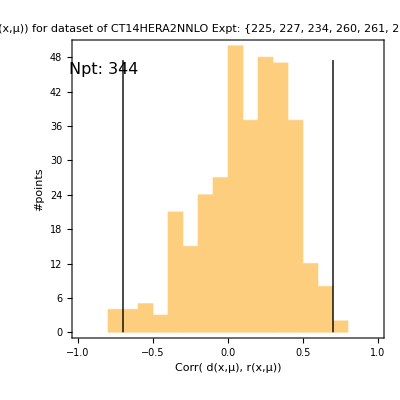
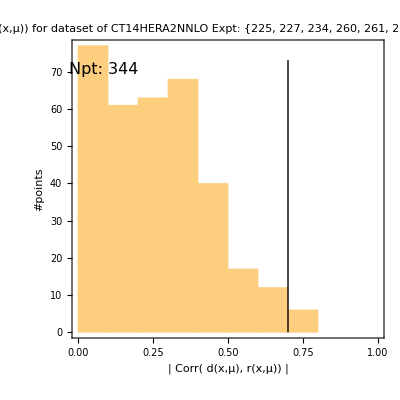
{{-Graphics-,Corr( d(x,μ), r(x,μ)) for dataset of
CT14HERA2NNLO

 |  | 
Data Sets |  | 
cdfLasy(225) | cdfLasy2(227) | d02Masy1(234)
ZyD02a(260) | ZyCDF2(261) | ATL7_WZ(268)
LHCb7_WZ1(240) | LHCb7Wasy1(241) | d02Easy5(281)
CMS7Masy2(266) | cdfLasy(225) | cdfLasy2(227)
d02Masy1(234) | ZyD02a(260) | ZyCDF2(261)
ATL7_WZ(268) | LHCb7_WZ1(240) | LHCb7Wasy1(241)
d02Easy5(281) | CMS7Masy2(266) | },{-Graphics-,-Graphics-}}

```mathematica
p6=processdataplotsmultiexp6percentageHere[corrdataclassfinal,readcorrconfigfile4[configDir,configfilename],6,2]
```

```mathematica
Lighter[Green,0.4]
```

RGBColor[0.4, 1., 0.4]

```mathematica
readcorrconfigfile4[configDir,configfilename]
```

{457,2017.0425.2123.-0500_ct14nn-new,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,542,544},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{0,0,0,1,0,1,0,1,0,0,0,1,0,0,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.00001,1},{1.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,2,2,1,1,1},{0.5,0.75,0.,0.15,1.,1.75,0.5,1.,0.5,100.,0.5,1.,0.45,0.75},{50,86.55,85,100,85,100,85,100,50,85,50,85,50,85}}

```mathematica
Opacity[0.5,Gray]
```

Opacity[0.5,GrayLevel[0.5]]

```mathematica
corrdataclassfinal[[2]];
```

expts: {{225,227,234,260,261,268,240,241,281,266},{225,227,234,260,261,268,240,241,281,266}}

unhilgtsize: 0.01

size: medium

making table of experiments included in plots

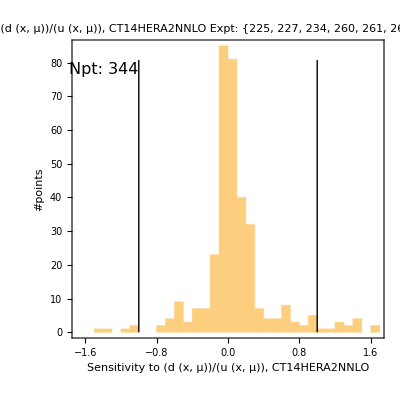
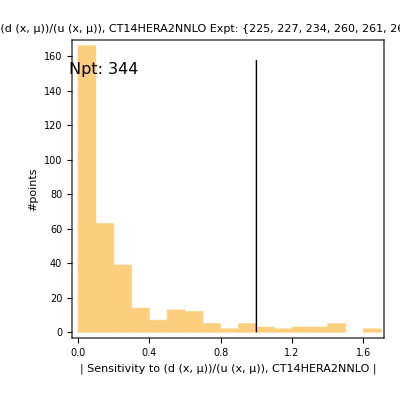
{{-Graphics-,Sensitivity to (d (x, μ))/(u (x, μ)), CT14HERA2NNLO

 |  | 
Data Sets |  | 
cdfLasy(225) | cdfLasy2(227) | d02Masy1(234)
ZyD02a(260) | ZyCDF2(261) | ATL7_WZ(268)
LHCb7_WZ1(240) | LHCb7Wasy1(241) | d02Easy5(281)
CMS7Masy2(266) | cdfLasy(225) | cdfLasy2(227)
d02Masy1(234) | ZyD02a(260) | ZyCDF2(261)
ATL7_WZ(268) | LHCb7_WZ1(240) | LHCb7Wasy1(241)
d02Easy5(281) | CMS7Masy2(266) | },{-Graphics-,-Graphics-}}

```mathematica
p5=processdataplotsmultiexp6percentageHere[dRcorrdataclassfinal,readcorrconfigfile4[configDir,configfilename],5,7]
```

change PDFsetname

expts: {{225,227,241,266,246},{225,227,241,266,246}}

unhilgtsize: 0.01

size: medium

can not find expt id = 246 in lisTable

can not find expt id = 246 in lisTable

making table of experiments included in plots

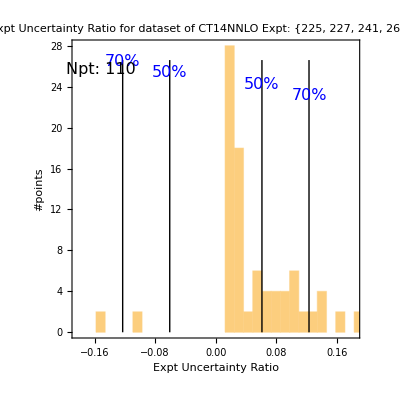
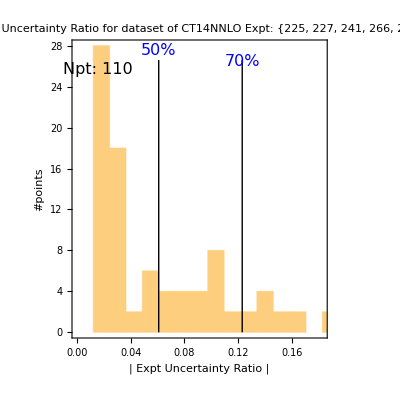
{{-Graphics-,Expt Uncertainty Ratio for dataset of
CT14NNLO

 |  | 
Data Sets |  | 
cdfLasy(225) | cdfLasy2(227) | LHCb7Wasy1(241)
CMS7Masy2(266) | None(246) | cdfLasy(225)
cdfLasy2(227) | LHCb7Wasy1(241) | CMS7Masy2(266)
None(246) |  | },{-Graphics-,-Graphics-}}

```mathematica
p234=processdataplotsmultiexp6percentageHere[{expterrordataclassfinal[[1]],#[[2+6]]&/@expterrordataclassfinal[[2]]},readcorrconfigfile4[configDir,configfilename],2,2]
```

change PDFsetname

expts: {{225,227,241,266,246},{225,227,241,266,246}}

can not find expt id = 246 in lisTable

can not find expt id = 246 in lisTable

making table of experiments included in plots

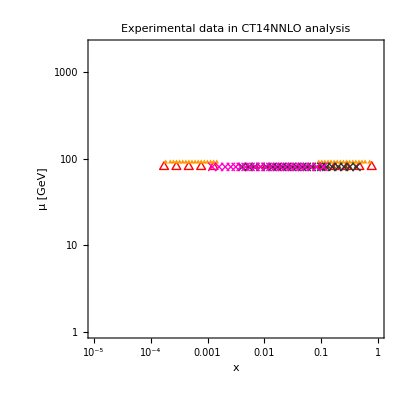

```mathematica
p1=processdataplotsmultiexp6percentageHere[corrdataclassfinal,readcorrconfigfile4[configDir,configfilename],1,0]
```

change PDFsetname

expts: {{225,227,241,266,246},{225,227,241,266,246}}

unhilgtsize: 0.01

size: medium

can not find expt id = 246 in lisTable

can not find expt id = 246 in lisTable

making table of experiments included in plots

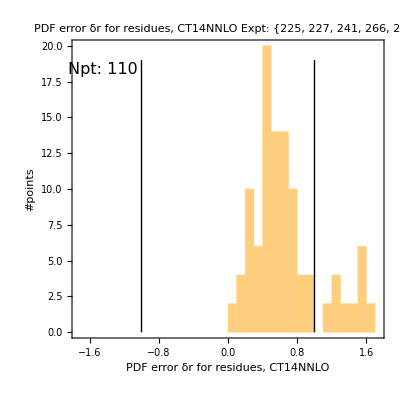
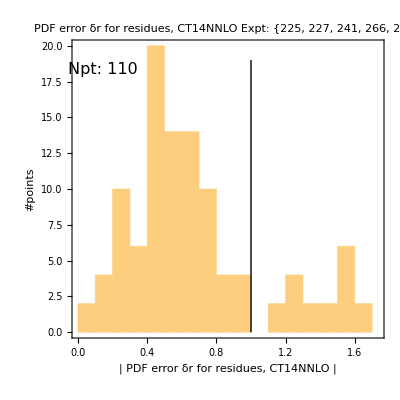
{{-Graphics-,PDF error δr for residues, CT14NNLO

 |  | 
Data Sets |  | 
cdfLasy(225) | cdfLasy2(227) | LHCb7Wasy1(241)
CMS7Masy2(266) | None(246) | cdfLasy(225)
cdfLasy2(227) | LHCb7Wasy1(241) | CMS7Masy2(266)
None(246) |  | },{-Graphics-,-Graphics-}}

```mathematica
p234=processdataplotsmultiexp6percentageHere[{dRdataclassfinal[[1]],#[[0+6]]&/@dRdataclassfinal[[2]]},readcorrconfigfile4[configDir,configfilename],4,0]
```

change PDFsetname

expts: {{225,227,241,266,246},{225,227,241,266,246}}

unhilgtsize: 0.01

size: medium

can not find expt id = 246 in lisTable

can not find expt id = 246 in lisTable

making table of experiments included in plots

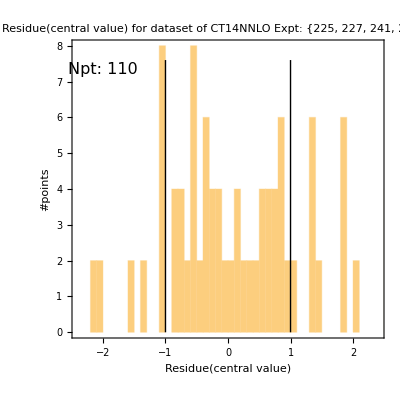
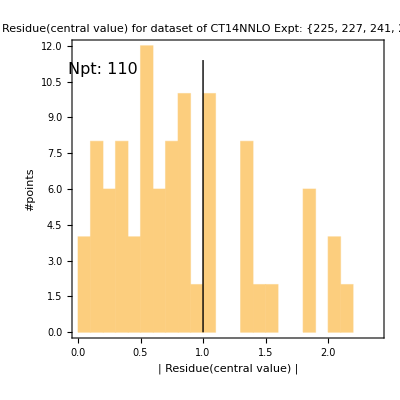
{{-Graphics-,Residue(central value) for dataset of
CT14NNLO

 |  | 
Data Sets |  | 
cdfLasy(225) | cdfLasy2(227) | LHCb7Wasy1(241)
CMS7Masy2(266) | None(246) | cdfLasy(225)
cdfLasy2(227) | LHCb7Wasy1(241) | CMS7Masy2(266)
None(246) |  | },{-Graphics-,-Graphics-}}

```mathematica
p234=processdataplotsmultiexp6percentageHere[{residualdataclassfinal[[1]],#[[1+6]]&/@residualdataclassfinal[[2]]},readcorrconfigfile4[configDir,configfilename],3,1]
```

```mathematica
Table[
corrdataclassfinal[[2,iexpt,flavour+6]][["data"]][[ix]][[3]],
{iexpt,1,Length[corrdataclassfinal[[2]] ]},{flavour,-5,-5+fmax-1},{ix,1,Length[corrdataclassfinal[[2,iexpt,flavour+6]][["data"]] ]}
];
listdelete=
Table[
If[Abs[corrdataclassfinal[[2,iexpt,flavour+6]][["data"]][[ix]][[3]] ]<0.7,True,False],
{iexpt,1,Length[corrdataclassfinal[[2]] ]},{flavour,-5,-5+fmax-1},{ix,1,Length[corrdataclassfinal[[2,iexpt,flavour+6]][["data"]] ]}
];

listdelete=
Table[
Position[listdelete[[iexpt,flavour+6]],True],
{iexpt,1,Length[corrdataclassfinal[[2]] ]},{flavour,-5,-5+fmax-1}
];

Table[
Delete[corrdataclassfinal[[2,iexpt,flavour+6]][["data"]],listdelete[[iexpt,flavour+6]] ],
{iexpt,1,Length[corrdataclassfinal[[2]] ]},{flavour,-5,-5+fmax-1}
];
```

```mathematica
listdelete;
```

```mathematica
corrdataclassfinal[[2]]
```

```mathematica
SetOptions[{Plot,ListPlot,Graphics,ParametricPlot},BaseStyle->{FontFamily->"Helvetica",16,Red}];
```

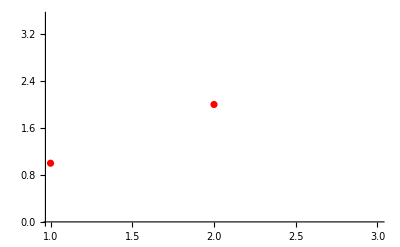

```mathematica
ListPlot[{{1,1},{2,2},{3,6}},FrameTicks->All,FrameTicksStyle->Red]
```